```mathematica
ClearAll["Global`*"];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../mathematica_utilities/mathematica_plot_options.nb"}]];
plot2Doption=Append[{PlotRange->All,PlotStyle->Red,Filling->Axis,GridLines->All,Joined->False},plot2Doption];
```

Available:plot2Doption
plot3Doption
framelabel[xlabel_String,ylabel_String,size_:20]
axeslabel2D[xlabel_String,ylabel_String,size_:20]
axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20]
axeslabel[labels_List,size_: 20]
importData
jsonInfo
interpolateAndFourier
interpolateAndFourierTr
MyFourier[list_,n_]
MyInverseFourier[list_,n_]
MyDiscreteConvolve[f_,g_]
MyDiscreteConvolveUsingCn[FourierGF_]
Rv[q_]
Rs[q_]
W2dQdt[q_,w_]
getOmegaFromKandDepth
getTFromLandDepth

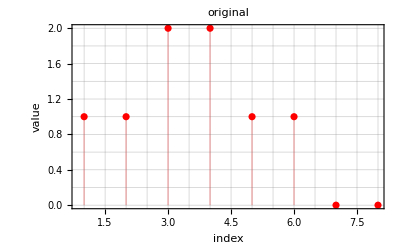

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_original_mathematica.png

```mathematica
casename="mathematica";

(*cosWave*)
If[casename=="mathematica",
list={1.,1.,2.,2.,1.,1.,0.,0.};
]

n=20;
(*cosWave*)
If[casename=="cosWave",
list=Table[Cos[2π/n*i],{i,0,n-1,1}];
]

(*squareWave*)
If[casename=="squareWave",
list=Flatten[Table[{Table[-1,{i,1,n/2,1}],Table[1,{i,1,n/2,1}]},{i,1,2}]];
]

(*triangleWave*)
If[casename=="triangleWave",
halfWave=Join[Table[i,{i,-1,1,2/(n-1)}],Table[i,{i,1,-1,-2/(n-1)}][[2;;-2]]];
list=Flatten[{halfWave,halfWave}];
]

(*list=Table[Cos[2π/n*i]*Cos[5π/n*i],{i,0,n-1,1}];*)
fig=ListPlot[list,PlotLabel->"original",FrameLabel->{"index","value"},GridLines->All, Joined->False,Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_original_"<>casename<>".png"}],fig]
```

```mathematica
Column[N@list,Frame->All]
num=30
(*list=Flatten@{Table[1,{i,1,num}],Table[2,{i,1,num}]}*)
(*list=Table[Cos[2π*i/num],{i,0,num-1}]*)

Grid[#,Frame->All]&@
{{"組み込みDFT","ユーザー定義DFT"},
{Column[Fourier[list,FourierParameters->{-1,-1}],Frame->All],
Column[cn=Table[MyFourier[list,n],{n,0,Length[list]-1}],Frame->All]}}
```

1.
1.
2.
2.
1.
1.
0.
0.

30

組み込みDFT | ユーザー定義DFT
1.+0. ⅈ
-0.176777-0.426777 ⅈ
0.+0. ⅈ
0.176777+0.0732233 ⅈ
0.+0. ⅈ
0.176777-0.0732233 ⅈ
0.+0. ⅈ
-0.176777+0.426777 ⅈ | 1.
-0.176777-0.426777 ⅈ
0.+0. ⅈ
0.176777+0.0732233 ⅈ
0.
0.176777-0.0732233 ⅈ
0.+0. ⅈ
-0.176777+0.426777 ⅈ

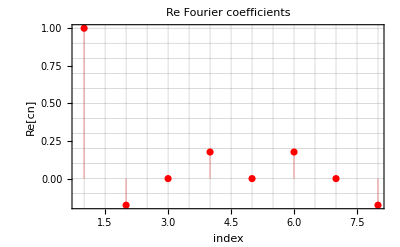

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Re_cn_mathematica.png

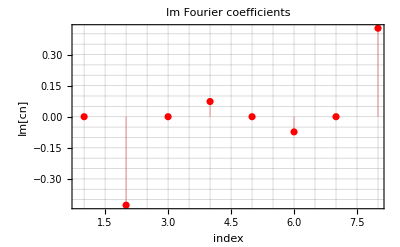

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Im_cn_mathematica.png

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_ReIm_cn_mathematica.png

```mathematica
figRe=ListPlot[Re[cn],PlotLabel->"Re Fourier coefficients",FrameLabel->{"index","Re[cn]"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Re_cn_"<>casename<>".png"}],figRe]

figIm=ListPlot[Im[cn],PlotLabel->"Im Fourier coefficients",FrameLabel->{"index","Im[cn]"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Im_cn_"<>casename<>".png"}],figIm]

Export[FileNameJoin[{NotebookDirectory[],"./sample_ReIm_cn_"<>casename<>".png"}],Row[{figRe,figIm}]]
```

InverseDFT | User defined InverseDFT
1.
1.
2.
2.
1.
1.
0.
-2.22045×10^-16 | 1.+0. ⅈ
1.+0. ⅈ
2.+0. ⅈ
2.+0. ⅈ
1.+0. ⅈ
1.+0. ⅈ
-1.66533×10^-16+0. ⅈ
0.+2.77556×10^-17 ⅈ

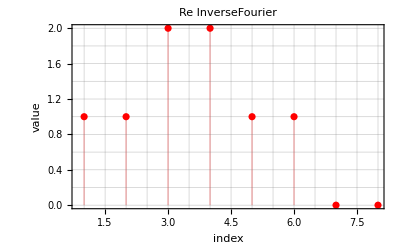

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Re_inv_mathematica.png

```mathematica
len=Length[list];

Grid[#,Frame->All]&@{{"InverseDFT","User defined InverseDFT"},
{Column[inv=InverseFourier[cn,FourierParameters->{-1,-1}],Frame->All],
Column[Table[MyInverseFourier[cn,n],{n,0,Length[list]-1,1}],Frame->All]}}

fig=ListPlot[Re[inv],PlotLabel->"Re InverseFourier",FrameLabel->{"index","value"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Re_inv_"<>casename<>".png"}],fig]
```

```mathematica
(*n-1->-1*)
(*n-2->-2*)
Floor[Length[cn]-1]
shift=If[EvenQ[(Length[cn]-1)/2],{(Length[cn]-1)/2,(Length[cn]-1)/2},{(Length[cn]-1+1)/2,(Length[cn]-1-1)/2}]
Do[Cn[i]=cn[[i+1]],{i,0,shift[[1]]}]
Do[Cn[-i]=cn[[Length[cn]+1-i]],{i,1,shift[[2]]}]
```

7

{4,3}

```mathematica
Column@Table[{i,Re@Cn[i]},{i,-shift[[2]],shift[[1]],1}]
```

{-3,0.176777}
{-2,0.}
{-1,-0.176777}
{0,1.}
{1,-0.176777}
{2,0.}
{3,0.176777}
{4,0.}

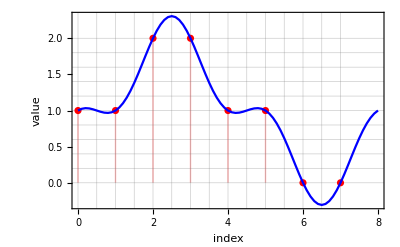

```mathematica
f[t_]:=With[{len=Length[list]},Sum[Cn[n]*Exp[I*n*2 π/len*t],{n,-shift[[2]],shift[[1]],1}]];
fig=Show[
ListPlot[Table[{i-1,list[[i]]},{i,1,Length[list],1}],FrameLabel->{"index","value"},Evaluate[plot2Doption]],
ListPlot[Table[{t,Re[f[t]]},{t,0,Length[list],0.1}],PlotStyle->Blue,Filling->None,Joined->True,Evaluate[plot2Doption]]
,PlotRange->All
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"./sample_interpolation_"<>casename<>".png"}],fig]
```

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_interpolation_mathematica.png

```mathematica
f[t_,expandmax_]:=With[{len=Length[list]},Sum[Cn[n]*Exp[I*n*2 π/len*t],{n,-expandmax,expandmax,1}]];
anim=Manipulate[
Show[
ListPlot[Table[{i-1,list[[i]]},{i,1,Length[list],1}],FrameLabel->{"index","value"},Evaluate[plot2Doption]],
ListPlot[Table[{t,Re[f[t,expandmax]]},{t,0,Length[list],0.1}],PlotStyle->Blue,Filling->None,Joined->True,Evaluate[plot2Doption]]
,PlotRange->All
,PlotLabel->expandmax
],{expandmax,1,Min[shift],1}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"./sample_convergence_"<>casename<>".gif"}],anim]
```

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_convergence_mathematica.gif

14

基本的畳み込み和

{0.000904,1.+1. ⅈ
1.+1. ⅈ
2.+2. ⅈ
1.+1. ⅈ
1.+1. ⅈ
0.+0. ⅈ
1.+1. ⅈ
0.+0. ⅈ
4.+4. ⅈ
3.+3. ⅈ
5.+5. ⅈ
1.+1. ⅈ
4.+4. ⅈ
2.+2. ⅈ}

効率的な畳み込み：離散フーリエ変換→積→逆離散フーリエ

{1.85714+1.85714 ⅈ,0.785708-1.43555 ⅈ,-0.209208-0.11964 ⅈ,-0.0869727+0.0665292 ⅈ,0.20983-0.103119 ⅈ,-0.0272876+0.0547192 ⅈ,-0.0503039-0.0847021 ⅈ,0.142857+0.142857 ⅈ,-0.0847021-0.0503039 ⅈ,0.0547192-0.0272876 ⅈ,-0.103119+0.20983 ⅈ,0.0665292-0.0869727 ⅈ,-0.11964-0.209208 ⅈ,-1.43555+0.785708 ⅈ}

{0.0714286,-0.0406094-0.0110608 ⅈ,0.0594598+0.14882 ⅈ,0.189139-0.0481908 ⅈ,-0.0859219-0.0978976 ⅈ,-0.0771012+0.226112 ⅈ,0.240748+0.239905 ⅈ,0.357143,0.240748-0.239905 ⅈ,-0.0771012-0.226112 ⅈ,-0.0859219+0.0978976 ⅈ,0.189139+0.0481908 ⅈ,0.0594598-0.14882 ⅈ,-0.0406094+0.0110608 ⅈ}

14

14

{0.000489,1.+1. ⅈ
1.+1. ⅈ
2.+2. ⅈ
1.+1. ⅈ
1.+1. ⅈ
1.94289×10^-15+1.94289×10^-15 ⅈ
1.+1. ⅈ
7.77156×10^-16+0. ⅈ
4.+4. ⅈ
3.+3. ⅈ
5.+5. ⅈ
1.+1. ⅈ
4.+4. ⅈ
2.+2. ⅈ}

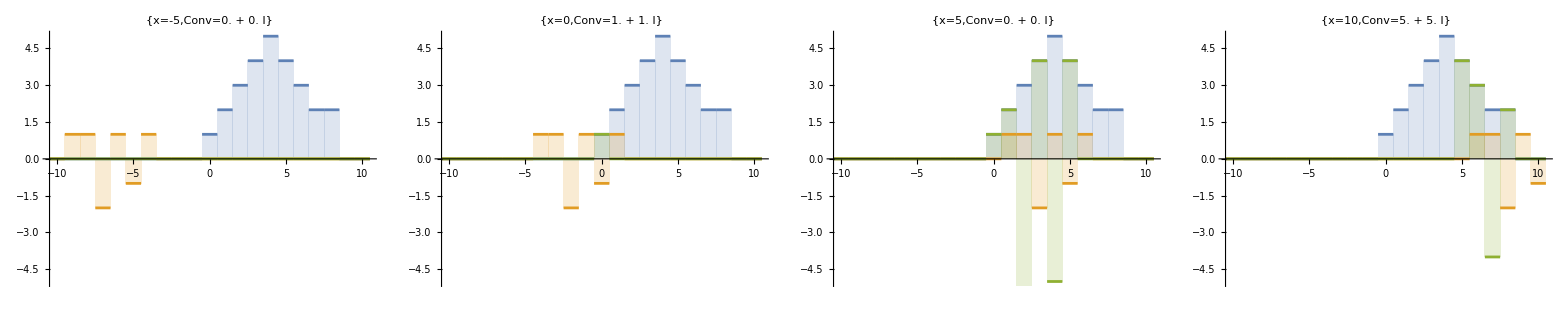

```mathematica
Clear["Global`*"];
Quiet@NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../mathematica_plot_options.nb"}]];

f=N@{1,2,3,4,5,4,3,2,2}+{1,2,3,4,5,4,3,2,2}*ⅈ;
g=N@{1,-1,1,-2,1,1};
len=Length[f]+Length[g]-1;

(*スライド変数xを変化させて畳み込み和を計算する．畳み込み和がゼロでないのは，x=14のときまでだ．*)
Length[{1*0,2*0,3*0,4*0,5*0,4*0,3*0,2*0,2*1,0*1,0*-2,0*1,0*-1,0*1}]
(*したがって，入力データの長さを14(周期のようなもの)に変えて，フーリエ係数を計算し，２つをかけ合わせ，逆フーリエ変換する*)

P[data_,j_]:=With[{i=j+1},Piecewise[{{data[[i]],Between[i,{1,Length[data]}]},{0,True}}]];

Print["基本的畳み込み和"]
AbsoluteTiming@Column[b=Table[N@Sum[P[f,i]*P[g,x-i],{i,0,len}],{x,0,len-1}],Frame->All]

Print["効率的な畳み込み：離散フーリエ変換→積→逆離散フーリエ"]
f=PadRight[f,len];
g=PadRight[g,len];
F=N@Table[MyFourier[f,n],{n,0,len-1}]
G=N@Table[MyFourier[g,n],{n,0,len-1}]
GF=G*F;
lenG=Length[G]
lenF=Length[F]
AbsoluteTiming@Column[Table[MyInverseFourier[GF,n],{n,0,len-1}],Frame->All]

Grid[{
Table[
DiscretePlot[
{
Re@P[f,i],
Re@P[g,x-i+1],
Re[P[f,i]*P[g,x-i]]
}
,{i,-10,10}
,ImageSize->200
,PlotRange->{All,{-5,5}}
,ExtentSize->Full
,PlotLabel->{"x="<>ToString@x,"Conv="<>ToString@Style[Sum[P[f,i]*P[g,x-i],{i,-5,10,1}]]}]
,{x,-5,10,5}]
}
,Frame->All]
```

```mathematica
(*離散フーリエ変換を予め計算しておき，積の計算と逆フーリエ変換だけを実行するだけなら，多くの場合，基本的な方法よりも高速に実行できるだろう*)
```